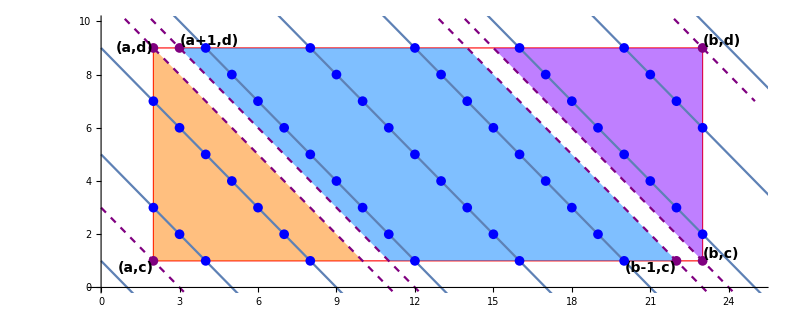

```mathematica
{x1,x2}={2,23};
{y1,y2}={1,9};
p=4;
m=1;

ticks[min_,max_]:=Table[i,{i,Ceiling[min],Floor[max],1}];
f=(k p+m)-x;
lines = Table[Plot[f,{x,0,x2+3}],{k,-1,((x2+3)+(y2+3))/2+4}];
points=Table[ListPlot[Select[Table[{x,f},{x,x1,x2}],Between[#[[2]],{y1,y2}]&],PlotStyle->Directive[Blue,AbsolutePointSize[7]]],{k,-1,((x2+3)+(y2+3))/2+4}];
rectangle=Graphics[{FaceForm[],EdgeForm[Directive[Red,Thick,Dashed]],Rectangle[{x1,y1},{x2,y2}]}];
areas=Graphics[{
{FaceForm[RGBColor[1,0.5,0,0.5]],Triangle[{{x1,y1},{x1,y2},{x1+(y2-y1),y1}}]},
{FaceForm[RGBColor[0.5,0,1,0.5]],Triangle[{{x2,y2},{x2,y1},{x2-(y2-y1),y2}}]},
If[x2-x1≠y2-y1,{FaceForm[RGBColor[0,0.5,1,0.5]],Parallelogram[{x1+1,y2},{{y2-y1,-(y2-y1)},{(x2-x1)-(y2-y1)-2,0}}]}]
}];
points2 = Graphics[{
{Purple,AbsolutePointSize[7],Point[{{x1,y1},{x2,y1},{x1,y2},{x2,y2}}]},
{Text[Style["(a,c)",14,Bold],{x1,y1},{1.5,1}]},
{Text[Style["(b,c)",14,Bold],{x2,y1},{-1.5,-1}]},
{Text[Style["(a,d)",14,Bold],{x1,y2},{1.5,0}]},
{Text[Style["(b,d)",14,Bold],{x2,y2},{-1.5,-1}]},
If[x2-x1≠ y2-y1,{
{Purple,AbsolutePointSize[7],Point[{{x1+1,y2},{x2-1,y1}}]},
{Text[Style["(a+1,d)",14,Bold],{x1+1,y2},{-1.2,-1.3}]},
{Text[Style["(b-1,c)",14,Bold],{x2-1,y1},{1.2,1.2}]}
}]
}];
lines2 = Table[Plot[-x+(a+b),{x,0,x2+2},PlotStyle->Directive[Dashed,Purple]],{a,{x1,x2}},{b,{y1,y2}}];
lines3 = If[x2-x1≠y2-y1,
Table[Plot[-x+b,{x,0,x2+2},PlotStyle->Directive[Dashed,Purple]],{b,{x1+1+y2,x2-1+y1}}],{}
];
Show[
rectangle,areas,lines,lines2,lines3,points2,points,
Axes->True,AxesOrigin->{0,0},AxesStyle->Directive[Black],PlotRange->{{0,x2+2},{0,y2+1}},AspectRatio->Automatic,GridLines->ticks,GridLinesStyle->Directive[Gray, Dashed],Ticks->ticks,ImageSize->800
]
```